```mathematica
f[z_] = z^(3/2)*(2/(π z))^(1/2)Exp[-I( z-π/4)]Exp[-z^2/(4 σ^2)];

complex = Simplify[Simplify[Abs[ComplexExpand[f[r Exp[I θ]]]], Assumptions->{σ>0, r>0, θ>0}]/. Arg[ⅇ^(-ⅈ θ)]-> -θ/. Arg[ⅇ^(ⅈ θ)]-> θ, Assumptions->{θ>0}]*Exp[-(2 π)/h r Sin[θ]]/(Abs[Cos[θ]+ⅈ Sin[θ]])
```

ⅇ^(-(r^2 Cos[2 θ])/(4 σ^2)+r Sin[θ]-(2 π r Sin[θ])/h) √(2/π) r

```mathematica
Simplify[complex/.r-> Sqrt[x^2+y^2]/.θ-> ArcTan[y/x], Assumptions->{x>0,y>0,σ>0,h>0}]
```

ⅇ^(y-(2 π y)/h-x^2/(4 σ^2)+y^2/(4 σ^2)) √(2/π) √(x^2+y^2)

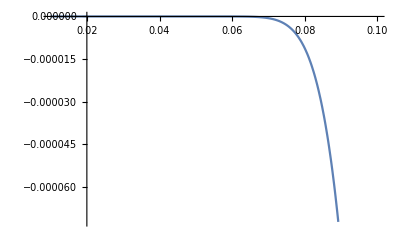

```mathematica
Plot[(ⅇ^(y-(2 π y)/h+y^2/(4 σ^2)) √(2/π) Integrate[ⅇ^(-x^2/(4 σ^2))√(x^2+y^2), {x, Infinity, -Infinity}, Assumptions->{σ>0,y>0}])/.y-> 0.04 σ^2((2 π)/h-1)/.σ-> 0.2, {h,0.01, 0.1}]
```

```mathematica
integrated[y_,σ_,h_] = ⅇ^(y-(2 π y)/h+y^2/(4 σ^2)) √(2/π) Integrate[ⅇ^(-x^2/(4 σ^2))√(x^2+y^2), {x, Infinity, -Infinity}, Assumptions->{σ>0,y>0}]
```

-4 √2 ⅇ^(y-(2 π y)/h+y^2/(4 σ^2)) σ^2 HypergeometricU[-1/2,0,y^2/(4 σ^2)]

```mathematica
Simplify[(-4 √2 ⅇ^(y-(2 π y)/h+y^2/(4 σ^2)) σ^2 HypergeometricU[-1/2,0,y^2/(4 σ^2)])/.y-> 2*σ^2((2 π)/h-1), Assumptions->{h>0,σ>0}]
```

-4 √2 ⅇ^(-((h-2 π)^2 σ^2)/h^2) σ^2 HypergeometricU[-1/2,0,((h-2 π)^2 σ^2)/h^2]

```mathematica
Plot3D[ 2*σ^2((2 π)/h-1), {σ, 0,2}, {h, 0.01,0.1}]
```

```mathematica
Plot3D[(4 √2 ⅇ^(-((h-2 π)^2 σ^2)/h^2) σ^2 HypergeometricU[-1/2,0,((h-2 π)^2 σ^2)/h^2])/.h-> ArcSinh[(2 ArcTanh[x/(n π)])/π]/n/.x-> 20, {σ, 0, 2}, {n, 1,100}]
```

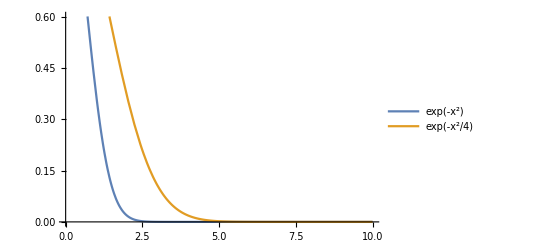

```mathematica
Plot[{Exp[-x^2], Exp[-1/4 x^2]}, {x, 0, 10}, PlotLegends->"Expressions"]
```

```mathematica
Plot3D[(ⅇ^(y-(2 π y)/h+y^2/(4 σ^2))HypergeometricU[-1/2,0,y^2/(4 σ^2)])/.σ-> 0.2, {h, 0.01, 0.1},{y, 0, (4*σ^2((2 π)/0.01-1))/.σ-> 0.2}, AxesLabel->{"h", "y", "f"}]
```

```mathematica
4/100 0.2^2((2 π)/0.001-1)//N
```

10.0515

```mathematica
integrated[4/100 0.2^2((2 π)/0.001-1),0.2,00.1]
```

-119298.

```mathematica
Integrated = Simplify[Integrate[Simplify[complex/.r-> Sqrt[x^2+y^2]/.θ-> ArcTan[y/x], Assumptions->{x>0,y>0,σ>0,h>0}], {x, Infinity, -Infinity}, Assumptions->{y>0,σ>0,h>0}]+
Integrate[Simplify[complex/.r-> Sqrt[x^2+y^2]/.θ-> -ArcTan[y/x], Assumptions->{x>0,y>0,σ>0,h>0}], {x, Infinity, -Infinity}, Assumptions->{y>0,σ>0,h>0}], Assumptions->{y>0,σ>0,h>0}]
```

```mathematica
Solve[x == π n Tanh[π/2 Sinh[h n]], h]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{h→ArcSinh[(2 ArcTanh[x/(n π)])/π]/n}}

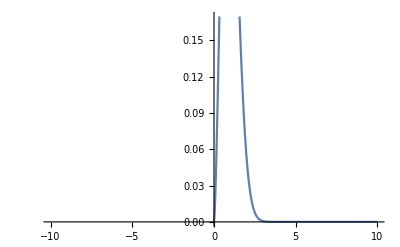

```mathematica
Plot[x^(3/2) Exp[-x^2], {x, -10,10}]
```

```mathematica
f[z_] = 1/Sqrt[z] Exp[-I(z- π/4)];
u[r_, θ_] = Simplify[Re[ComplexExpand[f[r Exp[I θ]]]], Assumptions->{r>0,θ>0}]/.Arg[ⅇ^(ⅈ θ)]-> θ
v[r_, θ_] = Simplify[Im[ComplexExpand[f[r Exp[I θ]]]], Assumptions->{r>0,θ>0}]/.Arg[ⅇ^(ⅈ θ)]-> θ
```

(ⅇ^(r Sin[θ]) (Cos[θ/2+r Cos[θ]]+Sin[θ/2+r Cos[θ]]))/(√2 √r)

(ⅇ^(r Sin[θ]) (Cos[θ/2] Cos[π/4+r Cos[θ]]-Sin[θ/2] Sin[π/4+r Cos[θ]]))/(√r)

```mathematica
Simplify[D [u[r,θ], r]-1/r D [v[r,θ], θ], Assumptions->{σ>0, r>0, θ>0}]
Simplify[D [v[r,θ], r]+1/r D [u[r,θ], θ], Assumptions->{σ>0, r>0, θ>0}]
```

0

0

```mathematica
Limit[Simplify[Integrate[(1/Sqrt[z] Cos[z-π/4])/.z-> r Exp[I θ], {θ, 0, 2 π}, Assumptions->{r>0}], Assumptions->{r>0}], r-> Infinity]
Limit[Simplify[Integrate[(1/Sqrt[z](Exp[-I(z-π/4)]+Exp[I(z-π/4)]))/.z-> r Exp[I θ], {θ, 0, 2 π}, Assumptions->{r>0}], Assumptions->{r>0}], r-> Infinity]
```

0

0

```mathematica
Limit[%107, r-> Infinity]
```

4 √π

```mathematica
f[z_] = z Tanh[π/2 Sinh[z]]
```

z Tanh[1/2 π Sinh[z]]

```mathematica
Simplify[Sqrt[ComplexExpand[f[r Exp[I θ]]*f[r Exp[-I θ]]]], Assumptions->{r>0}]
```

r √(Tanh[1/2 π Sinh[r (Cos[θ]-ⅈ Sin[θ])]] Tanh[1/2 π Sinh[r (Cos[θ]+ⅈ Sin[θ])]])

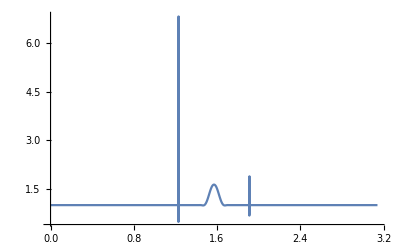

```mathematica
Plot[√(Tanh[1/2 π Sinh[r (Cos[θ]-ⅈ Sin[θ])]] Tanh[1/2 π Sinh[r (Cos[θ]+ⅈ Sin[θ])]])/.r-> 15,{θ, 0, π} ]
```

```mathematica
Limit[√(Tanh[1/2 π Sinh[r (Cos[θ]-ⅈ Sin[θ])]] Tanh[1/2 π Sinh[r (Cos[θ]+ⅈ Sin[θ])]]), r-> Infinity]
```

Limit[√(Tanh[1/2 π Sinh[r (Cos[θ]-ⅈ Sin[θ])]] Tanh[1/2 π Sinh[r (Cos[θ]+ⅈ Sin[θ])]]),r→∞]

```mathematica
√(Tanh[1/2 π Sinh[r (Cos[θ]-ⅈ Sin[θ])]] Tanh[1/2 π Sinh[r (Cos[θ]+ⅈ Sin[θ])]])/.θ-> π
```

√(Tanh[1/2 π Sinh[r]]^2)

```mathematica
Simplify[Sqrt[Simplify[f'[z]/.z-> r Exp[I θ]*f'[z]/.z-> r Exp[-I θ], Assumptions->{r>0,θ>0}]], Assumptions->{r>0,θ>0}]/.θ-> π/2
```

√(1/4 π r Cosh[1/2 r Sec[1/2 π Sin[r]]^2 (π r Cos[r]+Sin[π Sin[r]])] Sec[1/2 π Sin[r]]^2 Sech[1/2 π Sinh[1/2 r Sec[1/2 π Sin[r]]^2 (π r Cos[r]+Sin[π Sin[r]])]]^2 (π r Cos[r]+Sin[π Sin[r]])+Tanh[1/2 π Sinh[1/2 r Sec[1/2 π Sin[r]]^2 (π r Cos[r]+Sin[π Sin[r]])]])

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

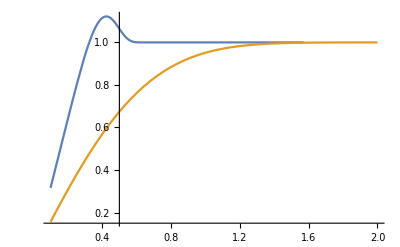

```mathematica
Plot[{%144, Tanh[π/2 Sinh[r]]}, {r, 0.1, 2}]
```

```mathematica
Plot[Sqrt[BesselJ[0,z Tanh[π/2 Sinh[z]]/.z-> r Exp[I θ]]BesselJ[0,z Tanh[π/2 Sinh[z]]/.z-> r Exp[-I θ]]]/.θ-> π/2,{r, 0, 200}]
```

```mathematica
Simplify[(z Tanh[π/2 Sinh[z]])/.z-> r Exp[I θ] (z Tanh[π/2 Sinh[z]])/.z-> r Exp[-I θ], Assumptions->{r>0,θ>0}]
```

r^2 Tanh[1/2 π Sinh[ⅇ^(-ⅈ θ) r]] Tanh[1/2 π Sinh[r^2 Tanh[1/2 π Sinh[ⅇ^(-ⅈ θ) r]]]]

```mathematica
Simplify[ComplexExpand[(1/Sqrt[z] Exp[-I(z-π/4)]/.z-> t Tanh[π/2 Sinh[t]])/.t-> r Exp[I θ]*(1/Sqrt[z] Exp[-I(z-π/4)]/.z-> t Tanh[π/2 Sinh[t]])/.t-> r Exp[-I θ]], Assumptions->{r>0, θ>0}]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

$Aborted

```mathematica
ComplexExpand[Tanh[π/2 Sinh[r Exp[I θ]]]Tanh[π/2 Sinh[Exp[r Exp[-I θ]]]]]
```

Abs[(Sin[π Cosh[r Cos[θ]] Sin[r Sin[θ]]] Sin[π Cosh[ⅇ^(r Cos[θ]) Cos[r Sin[θ]]] Sin[ⅇ^(r Cos[θ]) Sin[r Sin[θ]]]])/((Cos[π Cosh[r Cos[θ]] Sin[r Sin[θ]]]+Cosh[π Cos[r Sin[θ]] Sinh[r Cos[θ]]]) (Cos[π Cosh[ⅇ^(r Cos[θ]) Cos[r Sin[θ]]] Sin[ⅇ^(r Cos[θ]) Sin[r Sin[θ]]]]+Cosh[π Cos[ⅇ^(r Cos[θ]) Sin[r Sin[θ]]] Sinh[ⅇ^(r Cos[θ]) Cos[r Sin[θ]]]]))+(Sinh[π Cos[r Sin[θ]] Sinh[r Cos[θ]]] Sinh[π Cos[ⅇ^(r Cos[θ]) Sin[r Sin[θ]]] Sinh[ⅇ^(r Cos[θ]) Cos[r Sin[θ]]]])/((Cos[π Cosh[r Cos[θ]] Sin[r Sin[θ]]]+Cosh[π Cos[r Sin[θ]] Sinh[r Cos[θ]]]) (Cos[π Cosh[ⅇ^(r Cos[θ]) Cos[r Sin[θ]]] Sin[ⅇ^(r Cos[θ]) Sin[r Sin[θ]]]]+Cosh[π Cos[ⅇ^(r Cos[θ]) Sin[r Sin[θ]]] Sinh[ⅇ^(r Cos[θ]) Cos[r Sin[θ]]]]))+ⅈ (-((Sin[π Cosh[ⅇ^(r Cos[θ]) Cos[r Sin[θ]]] Sin[ⅇ^(r Cos[θ]) Sin[r Sin[θ]]]] Sinh[π Cos[r Sin[θ]] Sinh[r Cos[θ]]])/((Cos[π Cosh[r Cos[θ]] Sin[r Sin[θ]]]+Cosh[π Cos[r Sin[θ]] Sinh[r Cos[θ]]]) (Cos[π Cosh[ⅇ^(r Cos[θ]) Cos[r Sin[θ]]] Sin[ⅇ^(r Cos[θ]) Sin[r Sin[θ]]]]+Cosh[π Cos[ⅇ^(r Cos[θ]) Sin[r Sin[θ]]] Sinh[ⅇ^(r Cos[θ]) Cos[r Sin[θ]]]])))+(Sin[π Cosh[r Cos[θ]] Sin[r Sin[θ]]] Sinh[π Cos[ⅇ^(r Cos[θ]) Sin[r Sin[θ]]] Sinh[ⅇ^(r Cos[θ]) Cos[r Sin[θ]]]])/((Cos[π Cosh[r Cos[θ]] Sin[r Sin[θ]]]+Cosh[π Cos[r Sin[θ]] Sinh[r Cos[θ]]]) (Cos[π Cosh[ⅇ^(r Cos[θ]) Cos[r Sin[θ]]] Sin[ⅇ^(r Cos[θ]) Sin[r Sin[θ]]]]+Cosh[π Cos[ⅇ^(r Cos[θ]) Sin[r Sin[θ]]] Sinh[ⅇ^(r Cos[θ]) Cos[r Sin[θ]]]])))]

```mathematica
Tanh[π/2 Sinh[r Exp[I θ]]]Tanh[π/2 Sinh[Exp[r Exp[-I θ]]]]/.r-> 2/.θ-> π/2//N
```

6.53929-14.0382 ⅈ

```mathematica
Simplify[Sqrt[Abs[Simplify[Re[ComplexExpand[Tanh[π/2 Sinh[r Exp[I θ]]]]], Assumptions->{r>0,π>θ>0}]]^2+Abs[Simplify[Im[ComplexExpand[Tanh[π/2 Sinh[r Exp[I θ]]]]], Assumptions->{r>0,π>θ>0}]]^2], Assumptions->{r>0,θ>0}]
```

√((Im[1/(Cos[π Cosh[r Cos[θ]] Sin[r Sin[θ]]]+Cosh[π Cos[r Sin[θ]] Sinh[r Cos[θ]]])]^2+Re[1/(Cos[π Cosh[r Cos[θ]] Sin[r Sin[θ]]]+Cosh[π Cos[r Sin[θ]] Sinh[r Cos[θ]]])]^2) (Sin[π Cosh[r Cos[θ]] Sin[r Sin[θ]]]^2+Sinh[π Cos[r Sin[θ]] Sinh[r Cos[θ]]]^2))

```mathematica
Plot3D[%202, {r,0.1,10}, {θ, 0.1,3}]
```

```mathematica
Simplify[Im[ComplexExpand[z Tanh[π/2 Sinh[z]]/.z-> (x+I y)]], Assumptions->{x>0,y>0}]
```

Im[1/(Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])] (-y Sin[π Cosh[x] Sin[y]]+x Sinh[π Cos[y] Sinh[x]])+Re[1/(Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])] (x Sin[π Cosh[x] Sin[y]]+y Sinh[π Cos[y] Sinh[x]])

```mathematica
Plot3D[%207,{x,-10,10},{y, 0, 60}]
```

```mathematica
Simplify[Abs[ComplexExpand[z Tanh[π/2 Sinh[z]]/.z-> (x+I y)]], Assumptions->{Element[{x,y}, Reals]}]
```

Abs[(x+ⅈ y) Tanh[1/2 π Sinh[x+ⅈ y]]]

```mathematica
Plot3D[Abs[ Tanh[1/2 π Sinh[x+ⅈ y]]],{x,-20,20},{y, 0, 50}]
```

-Graphics3D-

```mathematica
Simplify[Cosh[x]^2-Sinh[x]^2, Assumptions->{x>0}]
```

1

```mathematica
Solve[u == Sinh[z], z]
```

{{z→ConditionalExpression[ⅈ π-ArcSinh[u]+2 ⅈ π C[1],C[1]∈Integers]},{z→ConditionalExpression[ArcSinh[u]+2 ⅈ π C[1],C[1]∈Integers]}}

```mathematica
D[ArcSinh[2/π u],u]
```

2/(π √(1+(4 u^2)/π^2))

```mathematica
Tanh[r Exp[I π/4]]/.r-> 100//N
```

1.-3.78947×10^-63 ⅈ

```mathematica
Solve[z Tanh[π/2 Sinh[z]] == u, z]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[z Tanh[1/2 π Sinh[z]]==u,z]

```mathematica
Simplify[z Tanh[π/2 Sinh[z]]//Expand ]
```

z Tanh[1/2 π Sinh[z]]

```mathematica
FunctionExpand[z Tanh[π/2 Sinh[z]] ]
```

z Tanh[1/2 π Sinh[z]]

```mathematica
Exp[π Sinh[z]](Exp[Log[z]]-Exp[Log[b]]) == Exp[Log[z]]+Exp[Log[b]]
```

```mathematica
Solve[Tanh[π/2 Sinh[z]] == u,z]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→ArcSinh[(2 ArcTanh[u])/π]}}

```mathematica
Plot3D[Abs[(x+I y)Tanh[π/2 Sinh[(x+I y)]]], {x,-5,5},{y,-10,10}]
```

-Graphics3D-

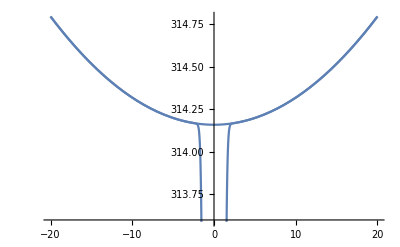

```mathematica
Plot[{Abs[(x+I y)Tanh[π/2 Sinh[(x+I y)]]],Abs[x+I y]}/.y-> 100 π, {x,-20,20}]
```

```mathematica
Plot[{Abs[BesselJ[0,(x+I y)/.y-> 20 π]],Abs[BesselJ[0,((x+I y)Tanh[π/2 Sinh[(x+I y)]])/.y->20 π]] }, {x,-10,10}]
```

-Graphics-

```mathematica
Plot[{Abs[BesselJ[0,((x+I y)Tanh[π/2 Sinh[(x+I y)]])/.y->20 π]] }, {x,-10,10}]
```

-Graphics-

```mathematica
Plot[{Abs[BesselJ[0,(x+I y)/.y-> 20 π]],Abs[BesselJ[0,((x+I y)Tanh[π/2 Sinh[(x+I y)]])/.y->20 π]] }, {x,-10,10}]
```

```mathematica
Plot[{Abs[(x+I y)^(3/2)Exp[-(x+I y)^2/(4 σ^2)]],Abs[((x+I y)Tanh[π/2 Sinh[(x+I y)]])^(3/2)Exp[-((x+I y)Tanh[π/2 Sinh[(x+I y)]])^2/(4 σ^2)]]}/.y-> 20 π/.σ-> 2, {x, -10,10}]
```

-Graphics-

```mathematica
Plot[{Abs[((x+I y)Tanh[π/2 Sinh[(x+I y)]])^(3/2)Exp[-((x+I y)Tanh[π/2 Sinh[(x+I y)]])^2/(4 σ^2)]]}/.y-> 20 π/.σ-> 2, {x, -10,10}]
```

-Graphics-

```mathematica
Solve[u == z(1-Exp[-π Sinh[z]]),z]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[u==(1-ⅇ^(-π Sinh[z])) z,z]

```mathematica
D[Tanh[π/2 Sinh[z+α z]],α]
```

1/2 π z Cosh[z+z α] Sech[1/2 π Sinh[z+z α]]^2

```mathematica
Solve[u == x^2/(x+ϵ),x]
```

{{x→1/2 (u-√u √(u+4 ϵ))},{x→1/2 (u+√u √(u+4 ϵ))}}

```mathematica
Series[x^2/(x(1+ ϵ)), {ϵ, 0, 1}]
```

x-x ϵ+O[ϵ]^2

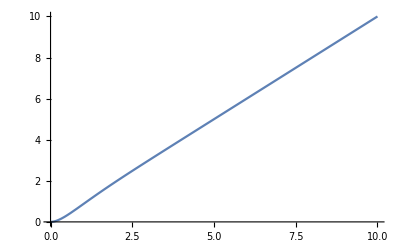

```mathematica
Plot[z(1-Exp[-2 z]), {z, 0, 10}]
```

```mathematica
Clear[u]
```

```mathematica
Reduce[u ==  t Tanh[π/2 Sinh[t]],{u,t} ]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[u==t Tanh[1/2 π Sinh[t]],{u,t}]

```mathematica
Limit[Simplify[Im[ComplexExpand[(R+I δ) Tanh[1/2 π Sinh[(R+I δ)]]]], Assumptions->{r>0, δ>0}], R-> Infinity]
```

Limit[Im[(-δ Sin[π Cosh[R] Sin[δ]]+R Sinh[π Cos[δ] Sinh[R]])/(Cos[π Cosh[R] Sin[δ]]+Cosh[π Cos[δ] Sinh[R]])]+Re[(R Sin[π Cosh[R] Sin[δ]]+δ Sinh[π Cos[δ] Sinh[R]])/(Cos[π Cosh[R] Sin[δ]]+Cosh[π Cos[δ] Sinh[R]])],R→∞]

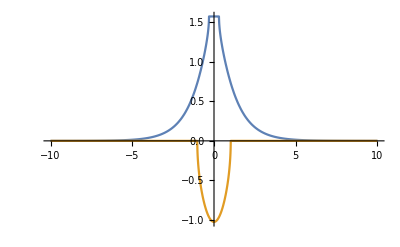

```mathematica
Plot[{Re[ArcSin[(π/3)/Cosh[x]]],Im[ArcSin[(π/2)/Cosh[x]]]}, {x, -10,10}, PlotRange->All]
```

```mathematica
Cosh[0]
```

1

```mathematica
Cosh[x]^2-Sinh[x]^2
```

Cosh[x]^2-Sinh[x]^2

```mathematica
Simplify[Cosh[x]^2-Sinh[x]^2]
```

1

```mathematica
Simplify[Tanh[(x+I π/2+n π)], Assumptions->{Element[n,Integers]}]
```

Coth[n π+x]

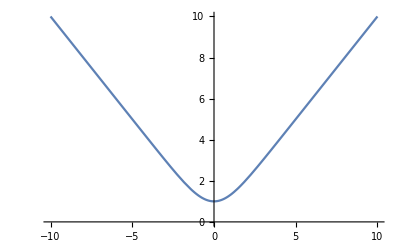

```mathematica
Plot[x*Coth[x], {x,-10,10}]
```

```mathematica
Solve[u == x Coth[x],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[u==x Coth[x],x]

```mathematica
Integrate[Abs[BesselJ[0,x]*x Exp[-x^2/(4 σ^2)]], {x,-Infinity,Infinity}, Assumptions->{σ>0}]
```

Integrate[ⅇ^(-1/4 Re[x^2/σ^2]) Abs[x BesselJ[0,x]],{x,-∞,∞},Assumptions→{σ>0}]

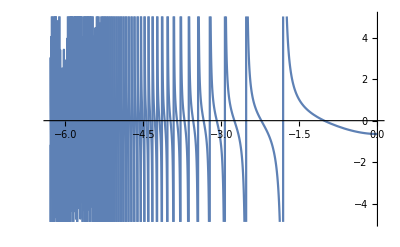

```mathematica
Plot[Im[Coth[I Cosh[x]]], {x,-2 π,0}]
```

```mathematica
Series[Coth[Sinh[x]],{x, 0, 1}]
```

1/x+x/6+O[x]^2

```mathematica
Integrate[1/u^(1/2)u Exp[-u^2], {u, 0, Infinity}]//N
```

0.612708

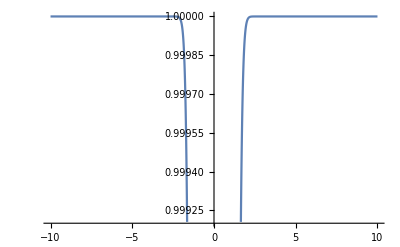

```mathematica
Plot[Abs[Tanh[π/2 Sinh[t]]], {t, -10,10}]
```

```mathematica
Series[HankelH2[0,I ϵ]/BesselJ[0,I ϵ], {ϵ, 0, 0}]
```

Floor[(π/2-Arg[ϵ])/(2 π)] (4+O[ϵ]^2)+(-(2 ⅈ (EulerGamma+ⅈ π-Log[2]+Log[ϵ]))/π+O[ϵ]^2)

```mathematica
Integrate[Exp[-x^2/(4 σ^2)-I x Sin[τ]], {τ,-Infinity, Infinity}, Assumptions->{σ>0, Element[τ,Reals]}]
```

Integrate[ⅇ^(-x^2/(4 σ^2)-ⅈ x Sin[τ]),{τ,-∞,∞},Assumptions→{σ>0,τ∈Reals}]

```mathematica
Integrate[Exp[-x^2+ α I x], {x,-Infinity,Infinity}]
```

ⅇ^(-α^2/4) √π

```mathematica
f[t_] = t Tanh[π/2 Sinh[t]]
Simplify[f[i π/4]]//N
```

t Tanh[1/2 π Sinh[t]]

0.785398 i Tanh[1.5708 Sinh[0.785398 i]]

```mathematica
0.7853981633974483 I*Tanh[1.5707963267948966Sinh[0.7853981633974483 I]//N]
```

-1.58492+0. ⅈ

```mathematica
π/4//N
```

0.785398

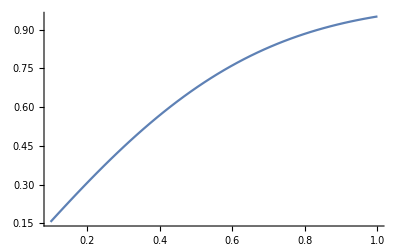

```mathematica
Plot[Abs[f[t]]/t, {t,0.1,1}]
```

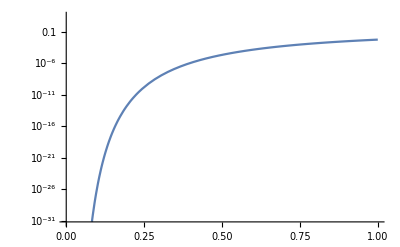

```mathematica
LogPlot[π/h Exp[-(2 π)/h], {h, 0.001, 1}]
```

```mathematica
Tanh[I (Sqrt[3] π)/4]//N
```

0.+4.68144 ⅈ

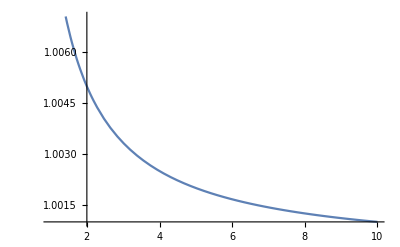

```mathematica
Plot[{(x+0.01)/x}, {x, 1, 10}]
```

```mathematica
Solve[u == (t^2+ϵ)/t, t]
```

{{t→1/2 (u-√(u^2-4 ϵ))},{t→1/2 (u+√(u^2-4 ϵ))}}

```mathematica
Simplify[Normal@Series[1/2 (u+√(u^2-4 ϵ)), {ϵ, 0, 1}], Assumptions->{u>0}]
```

u-ϵ/u

```mathematica
D[ t^2/(t+ ϵ), t]
```

-t^2/(t+ϵ)^2+(2 t)/(t+ϵ)

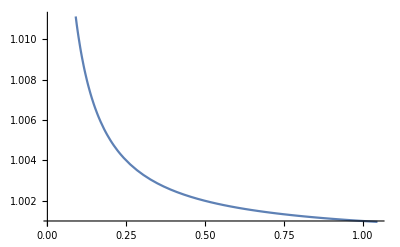

```mathematica
Plot[Abs[(t+ϵ)/t/.ϵ-> 0.001], {t, 0.01, π/3}]
```

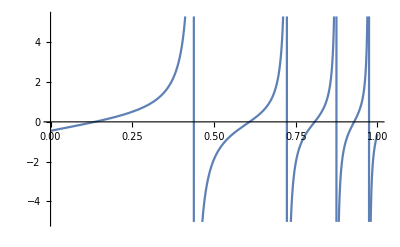

```mathematica
Plot[Tan[Exp[Exp[t]]], {t, 0, 1}]
```

```mathematica
Series[BesselJ[0,x+ϵ], {ϵ, 0, 1}]
```

BesselJ[0,x]-BesselJ[1,x] ϵ+O[ϵ]^2

```mathematica
Integrate[(x^2+y^2)^(1/4)Exp[-x^2/(4 σ^2)], {x, -Infinity,Infinity}, Assumptions->{y>0,σ>0}]
```

2 √(2 π) σ^(3/2) HypergeometricU[-1/4,1/4,y^2/(4 σ^2)]

```mathematica
Plot3D[((4 π)/h 1/Sqrt[2] σ^2 HypergeometricU[-1/2,0,y^2/(4 σ^2)]Exp[2 y +y^2/(4 σ^2)-(2 π)/h y])/.y-> π/3/.h-> 0.0083,{y,1,10},{σ,0.1,10}]
```

-Graphics3D-

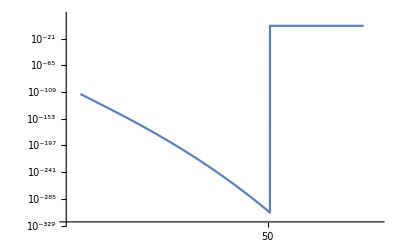

```mathematica
LogLogPlot[((4 π)/h 1/Sqrt[2] σ^2 HypergeometricU[-1/2,0,y^2/(4 σ^2)]Exp[2 y +y^2/(4 σ^2)-(2 π)/h y])/.y-> π/3/.σ-> 2/.h-> ArcSinh[(2 ArcTanh[100/(n π)])/π]/n, {n, 35, 60}]
```

```mathematica
Simplify[Exp[-(2 π^2)/(3 h)]/h/.h-> ArcSinh[(2 ArcTanh[x/(n π)])/π]/n,Assumptions->{x>0,n>0}]
```

(ⅇ^(-(2 n π^2)/(3 ArcSinh[(2 ArcTanh[x/(n π)])/π])) n)/ArcSinh[(2 ArcTanh[x/(n π)])/π]

```mathematica
Plot3D[ArcSinh[(2 ArcTanh[x/(n π)])/π]/n, {x,1,100},{n,1,100}]
```

-Graphics3D-

```mathematica
Solve[x == π n Tanh[π/2 Sinh[h n]], h]
```

{{h→ArcSinh[(2 ArcTanh[x/(n π)])/π]/n}}

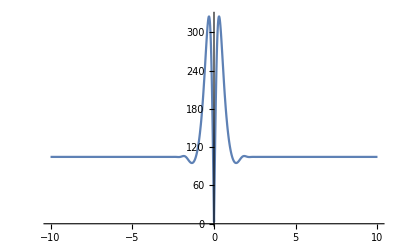

```mathematica
Plot[Abs[Im[ComplexExpand[(x+I y)Tanh[π/2 Sinh[(x+I y)]]]]/.y-> (100π)/3], {x, -10,10}, PlotRange->All]
```

```mathematica
Im[((x+I y)Tanh[π/2 Sinh[(x+I y)]])/.y-> π/3/.x-> 10//N]*3/π
```

1.

```mathematica
Simplify[Solve[x == π n(1-Exp[-2Exp[h n]]),h ], Assumptions->{n>0}]
```

{{h→ConditionalExpression[(2 ⅈ π C[1]+Log[1/2 (2 ⅈ π C[2]+Log[(n π)/(n π-x)])])/n,C[2]∈Integers&&C[1]∈Integers]}}

```mathematica
(((x+I y)Tanh[π/2 Sinh[(x+I y)]])/.x-> 10000/.y-> 0)//N
(((x+I y)Tanh[π/2 Sinh[(x+I y)]])/.x-> -10000/.y-> 0)//N
```

10000.

10000.

```mathematica
Im[ComplexExpand[(x+I y)Tanh[π/2 Sinh[(x+I y)]]]/.y-> π/3]
```

Im[-(π Sin[1/2 √3 π Cosh[x]])/(3 (Cos[1/2 √3 π Cosh[x]]+Cosh[1/2 π Sinh[x]]))+(x Sinh[1/2 π Sinh[x]])/(Cos[1/2 √3 π Cosh[x]]+Cosh[1/2 π Sinh[x]])]+Re[(x Sin[1/2 √3 π Cosh[x]])/(Cos[1/2 √3 π Cosh[x]]+Cosh[1/2 π Sinh[x]])+(π Sinh[1/2 π Sinh[x]])/(3 (Cos[1/2 √3 π Cosh[x]]+Cosh[1/2 π Sinh[x]]))]

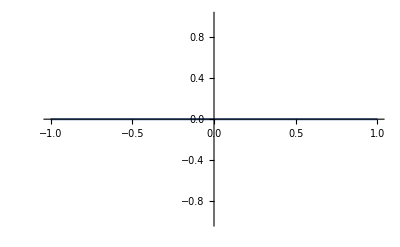

```mathematica
Plot[-Im[(x Sinh[π Cosh[x] Sinh[π/3]])/(Cosh[π Cosh[x] Sinh[π/3]]+Cosh[π Cosh[π/3] Sinh[x]])]-1/3 π Im[Sinh[π Cosh[π/3] Sinh[x]]/(Cosh[π Cosh[x] Sinh[π/3]]+Cosh[π Cosh[π/3] Sinh[x]])]+Im[(π Sinh[π Cosh[x] Sinh[π/3]])/(3 (Cosh[π Cosh[x] Sinh[π/3]]+Cosh[π Cosh[π/3] Sinh[x]]))+(x Sinh[π Cosh[π/3] Sinh[x]])/(Cosh[π Cosh[x] Sinh[π/3]]+Cosh[π Cosh[π/3] Sinh[x]])], {x, -1,1}]
```

```mathematica
(((x+I y)Tanh[π/2 Sinh[(x+I y)]])/.x-> 0/.y-> π/4)//N
(((x+I y)Tanh[π/2 Sinh[(x+I y)]])/.x-> 100/.y-> π/4)//N
```

-1.58492

100.+0.785398 ⅈ

```mathematica
π/4//N
```

0.785398

1000.79

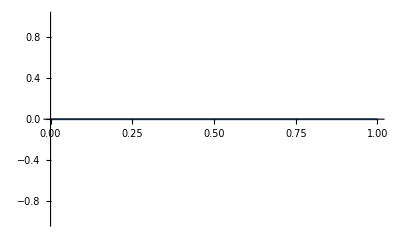

```mathematica
Plot[Im[ComplexExpand[Tanh[π/2 Sinh[(x+I y)]]]]/.y-> (I π)/3, {x,0,1}]
```

```mathematica
Plot3D[Re[(x+I y)Tanh[π/2(x+I y)]], {x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
Get["CustomTicks`"]
```

$Failed

```mathematica
Plot3D[Log10[σ^(3/2)HypergeometricU[-1/2,0,y^2/(4 σ^2)]Exp[2 Abs[y]+y^2/(4 σ^2)]], {y,-10,10},{σ,0,2}, PlotRange->Automatic]
```

-Graphics3D-

```mathematica
f[n_] := Integrate[LaguerreL[n,x]^2 Exp[-x],{x,0,Infinity}, Assumptions->{Element[n, Integers]}]
```

```mathematica
xlst = {}
ylst = {}
For[i=0,i<10,i++,AppendTo[xlst,i];AppendTo[ylst,f[i]]]
```

{}

{}

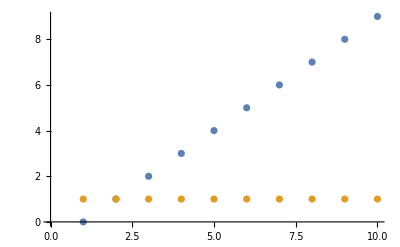

```mathematica
ListPlot[{xlst,ylst}]
```

```mathematica
Solve[LegendreP[2,x] == 0,x]//N
```

{{x→-0.57735},{x→0.57735}}

```mathematica
Plot[{f19[x],f20[x]},{x,0,50},PlotRange->All]
```

$Aborted

```mathematica
f1[x_] = 1/(1!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,1}];
f2[x_] = 1/(2!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,2}];
f3[x_] = 1/(3!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,3}];
f4[x_] = 1/(4!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,4}];
f5[x_] = 1/(5!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,5}];
f6[x_] = 1/(6!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,6}];
f7[x_] = 1/(7!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,7}];
f8[x_] = 1/(8!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,8}];
f9[x_] = 1/(9!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,9}];
f10[x_] = 1/(10!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,10}];
```

```mathematica
f11[x_] = 1/(1!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,11}];
f12[x_] = 1/(2!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,12}];
f13[x_] = 1/(3!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,13}];
f14[x_] = 1/(4!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,14}];
f15[x_] = 1/(5!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,15}];
f16[x_] = 1/(6!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,16}];
f17[x_] = 1/(7!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,17}];
f18[x_] = 1/(8!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,18}];
f19[x_] = 1/(9!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,19}];
f20[x_] = 1/(10!)D[x BesselJ[0,x] Exp[x-x^2/(4 2^2)],{x,20}];
```